# Phase Transition Quantities

## β/H

```mathematica
βHdata‵c30={Log10[#1],(#14)}&@@@Select[Import[NotebookDirectory[]<>"output/fix_ft_c30_out.csv"],Length[#]>13 &];
βH1ddata‵c30={Log10[#1],(#15)}&@@@Select[Import[NotebookDirectory[]<>"output/fix_ft_c30_out.csv"],Length[#]>13 &];
```

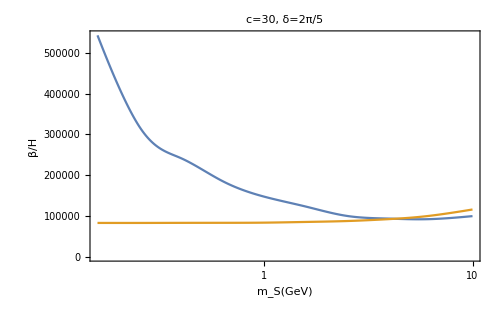

```mathematica
βHplot‵c30=ListLinePlot[βHdata‵c30,InterpolationOrder->3,BaseStyle->{FontSize->22,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S(GeV)",FontFamily->"Times",FontSize->22],Style["β/H",FontFamily->"Times",FontSize->24]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],ImageSize->500,FrameTicks->{{True,True},{LogTicks[-1,1,1],True}}];
βH1dplot‵c30=ListLinePlot[βH1ddata‵c30,InterpolationOrder->3,PlotStyle->ColorData[97,2]];
Show[βHplot‵c30,βH1dplot‵c30,PlotLabel->Style["c=30, δ=2π/5"],Epilog->{Inset[Framed[Column[{LineLegend[{ColorData[97,1],ColorData[97,2]},{"2d","1d"}]}],RoundingRadius->5],Scaled[{0.83,0.74}]]},Background->White,ImageSize->500,AspectRatio->1/GoldenRatio]
```

## T_n

```mathematica
TnTcdata‵c30={Log10[#1],(#12-#9)/#9*100}&@@@Select[Import[NotebookDirectory[]<>"output/fix_ft_c30_out.csv"],Length[#]>13 &];
Tn1dTcdata‵c30={Log10[#1],(#13-#9)/#9*100}&@@@Select[Import[NotebookDirectory[]<>"output/fix_ft_c30_out.csv"],Length[#]>13 &];
Tn1dTndata‵c30={Log10[#1],(#13-#12)/#9*100}&@@@Select[Import[NotebookDirectory[]<>"output/fix_ft_c30_out.csv"],Length[#]>13 &];
```

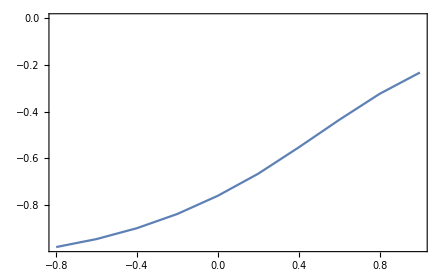

```mathematica
TnTcplot‵c30=ListLinePlot[TnTcdata‵c30]
```

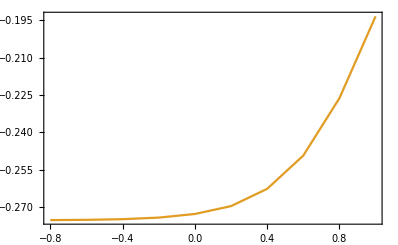

```mathematica
Tn1dTcplot‵c30=ListLinePlot[Tn1dTcdata‵c30,PlotStyle->ColorData[97,2]]
```

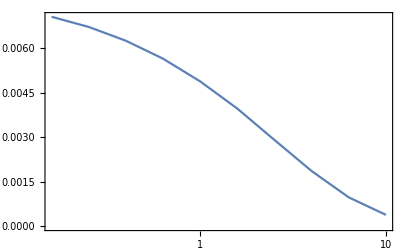

```mathematica
Tn1dTnplot‵c30=ListLinePlot[Tn1dTndata‵c30,FrameTicks->{{True,True},{LogTicks[-2,1,1],True}}]
```

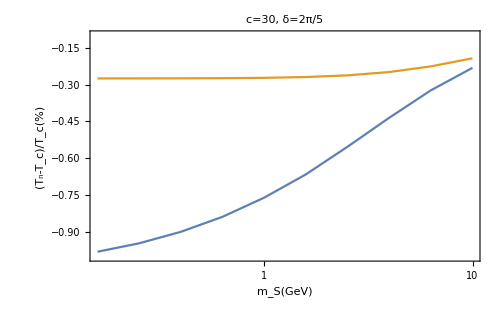

```mathematica
Show[TnTcplot‵c30,Tn1dTcplot‵c30,PlotRange->{Full,{-1,-0.1}},BaseStyle->{FontSize->22,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S(GeV)",FontFamily->"Times",FontSize->22],Style["(T_n-T_c)/T_c(%)",FontFamily->"Times",FontSize->24]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],ImageSize->500,FrameTicks->{{True,True},{LogTicks[-2,1,1],True}},Epilog->{Inset[Framed[Column[{LineLegend[{ColorData[97,1],ColorData[97,2]},{"2d","1d"}]}],RoundingRadius->5],Scaled[{0.85,0.25}]]},PlotLabel->Style["c=30, δ=2π/5"],Background->White,AspectRatio->1/GoldenRatio]
```